```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Show[
ListLinePlot[{{0.01,Log[pz[0.01,0,1.3,1,0.1]]},{0.1,Log[pz[0.1,0,1.3,1,0.1]]},{1,Log[pz[1,0,1.3,1,0.1]]},{2,Log[pz[2,0,1.3,1,0.1]]},{3,Log[pz[3,0,1.3,1,0.1]]}},PlotStyle->Red],
ListLinePlot[{{0.01,Log[pz[0.01,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{0.1,Log[pz[0.1,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{1,Log[pz[1,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{2,Log[pz[2,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{3,Log[pz[3,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]}},PlotStyle->Green],
ListLinePlot[{{0.01,Log[pz[0.01,qcrit[1.3,1,0.1],1.3,1,0.1]]},{0.1,Log[pz[0.1,qcrit[1.3,1,0.1],1.3,1,0.1]]},{1,Log[pz[1,qcrit[1.3,1,0.1],1.3,1,0.1]]},{2,Log[pz[2,qcrit[1.3,1,0.1],1.3,1,0.1]]},{3,Log[pz[3,qcrit[1.3,1,0.1],1.3,1,0.1]]}}]
,AxesLabel->{t,Log P}
]
]
```

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Show[
ListLinePlot[{{0.01,Log[pz[0.01,0,1.3,1,0.1]]},{0.1,Log[pz[0.1,0,1.3,1,0.1]]},{1,Log[pz[1,0,1.3,1,0.1]]},{2,Log[pz[2,0,1.3,1,0.1]]},{3,Log[pz[3,0,1.3,1,0.1]]}},PlotStyle->Red],
ListLinePlot[{{0.01,Log[pz[0.01,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{0.1,Log[pz[0.1,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{1,Log[pz[1,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{2,Log[pz[2,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{3,Log[pz[3,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]}},PlotStyle->Green],
ListLinePlot[{{0.01,Log[pz[0.01,qcrit[1.3,1,0.1],1.3,1,0.1]]},{0.1,Log[pz[0.1,qcrit[1.3,1,0.1],1.3,1,0.1]]},{1,Log[pz[1,qcrit[1.3,1,0.1],1.3,1,0.1]]},{2,Log[pz[2,qcrit[1.3,1,0.1],1.3,1,0.1]]},{3,Log[pz[3,qcrit[1.3,1,0.1],1.3,1,0.1]]}}]
,AxesLabel->{t,Log P}
]
]
```

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Block[
{f,r,l},
f[r_,l_]:=1+r^2/l^2;
EulerEquations[-Sqrt[-r'[t]^2/f[r[t],l]+f[r[t],l]],r[t],t]
]
```

(2 l^2 r[t]^3+r[t]^5+l^4 r[t] (1-3 r'[t]^2)+l^6 r''[t]+l^4 r[t]^2 r''[t])/(l^2 √(1+r[t]^2/l^2-(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0

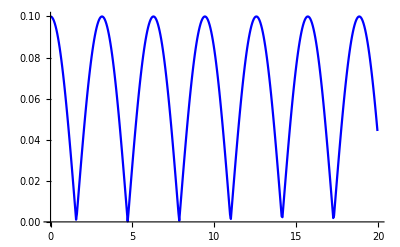

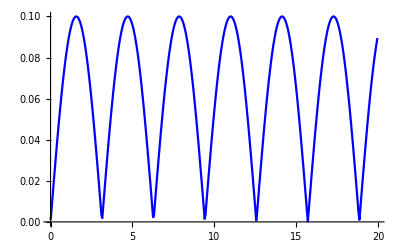

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_]:=NDSolveValue[{(2 l^2 r[t]^3+r[t]^5+l^4 r[t] (1-3 r'[t]^2)+l^6 r''[t]+l^4 r[t]^2 r''[t])/(l^2 √(1+r[t]^2/l^2-(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0/.{l->l1},r[0]==r1,r'[0]==0},r,{t,0.01,20}];
fr[l1_,r1_,t1_]:=rm[l1,r1][t1];
dr[l1_,r1_,t1_]:=D[rm[l1,r1][t],t]/.{t->t1};
pr[l1_,r1_,t1_]:=dr[l1,r1,t1]/Sqrt[-dr[l1,r1,t1]^2f[fr[l1,r1,t1],l1]+f[fr[l1,r1,t1],l1]^3];
Print[Show[
ListLinePlot[Table[{i,Abs[fr[1,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Blue],
AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[pr[1,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Blue],
AxesOrigin->{0,0}
]];
]
```

```mathematica
Abs[2]
```

2

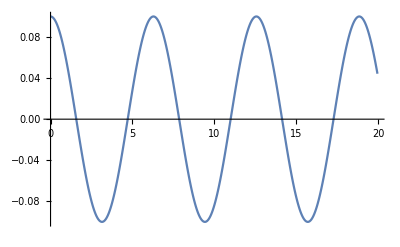

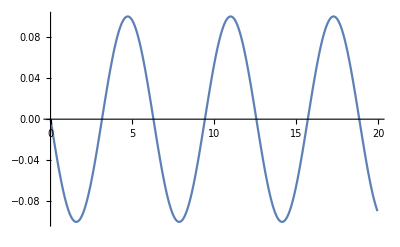

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_]:=NDSolveValue[{(2 l^2 r[t]^3+r[t]^5+l^4 r[t] (1-3 r'[t]^2)+l^6 r''[t]+l^4 r[t]^2 r''[t])/(l^2 √(1+r[t]^2/l^2-(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0/.{l->l1},r[0]==r1,r'[0]==0},r,{t,0.01,20}];
fr[l1_,r1_,t1_]:=rm[l1,r1][t1];
dr[l1_,r1_,t1_]:=D[rm[l1,r1][t],t]/.{t->t1};
pr[l1_,r1_,t1_]:=dr[l1,r1,t1]/Sqrt[-dr[l1,r1,t1]^2f[fr[l1,r1,t1],l1]+f[fr[l1,r1,t1],l1]^3];
Print[ListLinePlot[Table[{i,fr[1,0.1,i]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
Print[ListLinePlot[Table[{i,Re[pr[1,0.1,i]]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```

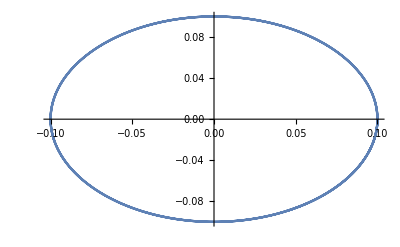

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_]:=NDSolveValue[{(2 l^2 r[t]^3+r[t]^5+l^4 r[t] (1-3 r'[t]^2)+l^6 r''[t]+l^4 r[t]^2 r''[t])/(l^2 √(1+r[t]^2/l^2-(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0/.{l->l1},r[0]==r1,r'[0]==0},r,{t,0.01,20}];
fr[l1_,r1_,t1_]:=rm[l1,r1][t1];
dr[l1_,r1_,t1_]:=D[rm[l1,r1][t],t]/.{t->t1};
pr[l1_,r1_,t1_]:=dr[l1,r1,t1]/Sqrt[-dr[l1,r1,t1]^2f[fr[l1,r1,t1],l1]+f[fr[l1,r1,t1],l1]^3];
Print[ListLinePlot[Table[{fr[1,0.1,i],Re[pr[1,0.1,i]]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```

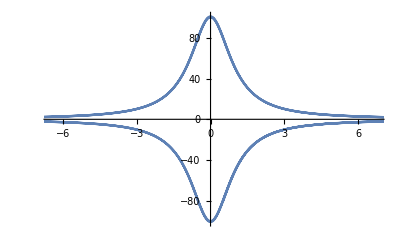

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_]:=NDSolveValue[{(2 l^2 r[t]^3+r[t]^5+l^4 r[t] (1-3 r'[t]^2)+l^6 r''[t]+l^4 r[t]^2 r''[t])/(l^2 √(1+r[t]^2/l^2-(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0/.{l->l1},r[0]==r1,r'[0]==0},r,{t,0.01,20}];
fr[l1_,r1_,t1_]:=rm[l1,r1][t1];
dr[l1_,r1_,t1_]:=D[rm[l1,r1][t],t]/.{t->t1};
pr[l1_,r1_,t1_]:=dr[l1,r1,t1]/Sqrt[-dr[l1,r1,t1]^2f[fr[l1,r1,t1],l1]+f[fr[l1,r1,t1],l1]^3];
Print[ListLinePlot[Table[{fr[1,100,i],Re[pr[1,100,i]]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```